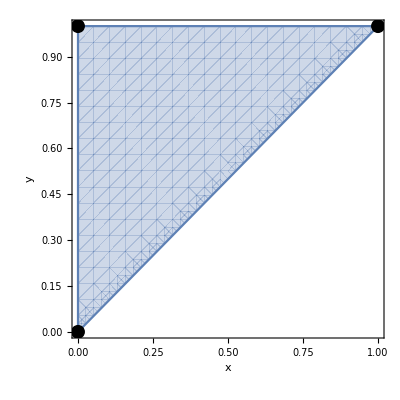

F:\Univ\_PhD\TA\MATH0462\Syllabus\2_2_implication.pdf

```mathematica
p=RegionPlot[x≤y,{x,0,1},{y,0,1},
FrameLabel->{Text@Style["x",FontSize->20],Rotate[Text@Style["y",FontSize->20],-90°]},
Epilog->{
PointSize[.025],
Point[{{0,0},{1,1},{0,1}}]
}]
Export[NotebookDirectory[]<>"2_2_implication.pdf",p]
```